## Presaditve ledvic

## Analiza presaditve ledvic

## Pridobivanje podatkov

Podatke sem pridobila iz podatkovne baze Wolfram data repository.

```mathematica
podatki = ResourceData["Sample Data: Kidney Transplant"]
```

## Analiza podatkov glede na spol, starost ter raso

Analizirala ter narisala bom nekaj grafov števila presaditve ledvic  glede na spol, starost ter raso. Podatki so obdelani ter predstavljeni tudi z nekaj grafi.

```mathematica
spolM = Length[Select[podatki,#["Gender"]=="male" &]]
```

524

```mathematica
spolZ= Length[Select[podatki,#["Gender"]=="female" &]]
```

339

### OBA SPOLA :

V seznamu z imenom seznamStarosti so zbrani podatki o starosti ljudi, ki so presadili ledvice. Podatki so prikazani tudi z histogramom.

```mathematica
seznamStarosti= podatki[All,"Age"]
```

Histrogram predstavlja podatke  glede na starost za oba spola.

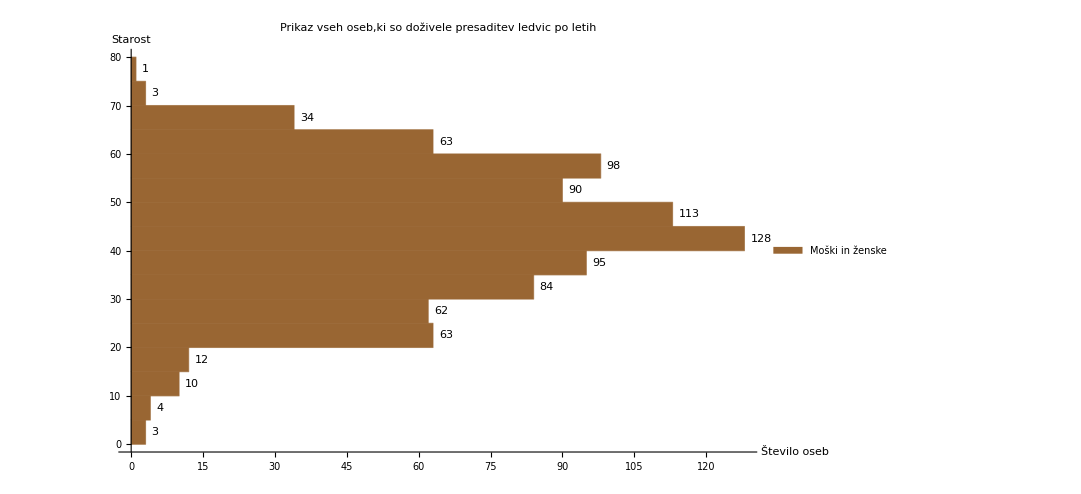

```mathematica
Histogram[seznamStarosti,ChartStyle->Brown, BarOrigin->Left,LabelingFunction->After,ImageSize->{800,550},ChartLegends->{"Moški in ženske"},PlotLabel->"Prikaz vseh oseb,ki so doživele presaditev ledvic po letih",AxesLabel->{"Število oseb","Starost"}]
```

### ŽENSKE :

V seznamu z imenom seznamZenske so zbrani podatki o starosti žensk in spodaj prikazani z histogramom.

```mathematica
seznamZenske =Select[podatki,#["Gender"]=="female" &][All,"Age"]
```

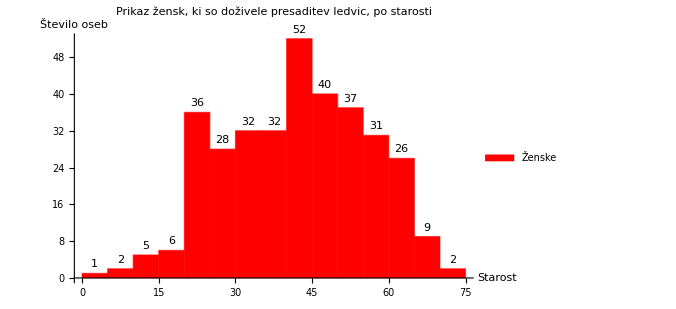

```mathematica
Histogram[seznamZenske,ChartLegends->{"Ženske"},ChartStyle->Red, LabelingFunction->Above,ImageSize->{500,300},PlotLabel->"Prikaz žensk, ki so doživele presaditev ledvic, po starosti",AxesLabel->{"Starost","Število oseb"}]
```

### MOŠKI :

V seznamu z imenom seznamMoski so zbrani podatki o starosti moških in spodaj prikazani z histogramom.

```mathematica
seznamMoski=Select[podatki,#["Gender"]=="male" &][All,"Age"]
```

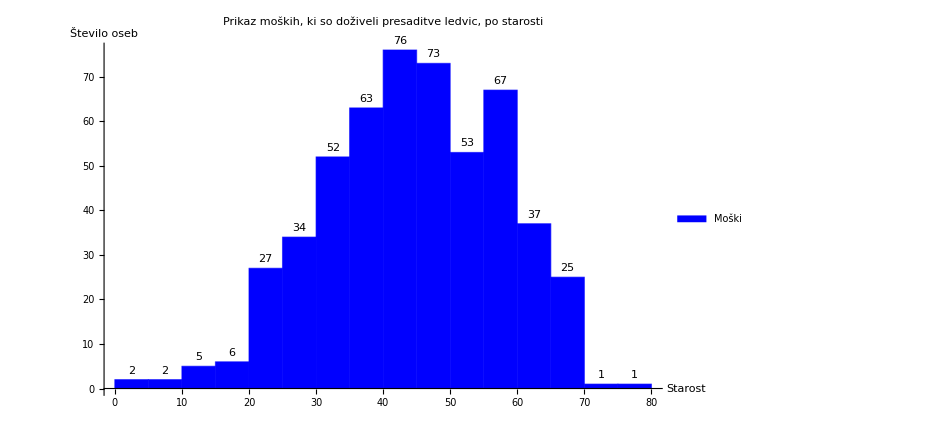

```mathematica
Histogram[seznamMoski,ChartLegends->{"Moški"},ChartStyle->Blue,LabelingFunction->Above,ImageSize->{700,500},PlotLabel->"Prikaz moških, ki so doživeli presaditve ledvic, po starosti",AxesLabel->{"Starost","Število oseb"}]
```

### RASA :

V funkciji SteviloRasa kot argument podamo raso in izpišemo število ljudi glede na raso. To funkcijo spodaj nato pokličem in ji kot argument podam vse rase.
Podatke o vseh  rasah shranim v seznam z imenom seznamPoRasah.

```mathematica
rase=podatki[All,"Race"]
```

```mathematica
SteviloRasa[rasa_]:={rasa,Count[rase,rasa]}
```

```mathematica
seznamPoRasah=SteviloRasa/@(rase //DeleteDuplicates)
```

Zgoraj zbrane podatke o rasah predstavim v obliki tortnega diagrama, ki ima tudi legendo, ki prikazuje katero barvo predstavlja katera rasa.

```mathematica
PieChart3D[Normal[seznamPoRasah[All,2]],ChartLegends->Normal[seznamPoRasah[All,1]],ImageSize->{400,400},ChartStyle->{Green,Purple,Yellow,Blue,Orange,Pink},PlotLabel->"Prikaz ljudi"]
```

-Graphics3D-

## Analiza glede na stanje po presaditvi:

```mathematica
seznamstanja=podatki[All,"Delta"]
```

```mathematica
umrli = Length[Select[podatki,#["Delta"]=="dead" &]]
```

140

```mathematica
preživeli = Length[Select[podatki,#["Delta"]=="alive" &]]
```

723

```mathematica
Podatke o stanju sem preštela in predstavila v obliki tortnega diagrama.
```

```mathematica
Stevilo[Delta_]:={Delta,Count [seznamstanja,Delta]}
```

```mathematica
seznampostanju=Stevilo/@(seznamstanja //DeleteDuplicates)
```

```mathematica
PieChart3D[Normal[seznampostanju[All,2]],ChartLegends->Normal[seznampostanju[All,1]],ImageSize->{400,400},ChartStyle->{Green,Purple},PlotLabel->"Prikaz ljudi, ki so umrli ali pa preživeli"]
```

-Graphics3D-

Analiza podatkov glede na čas.

```mathematica
seznamcas=podatki[All,"Time"]
```

```mathematica
Prešteti primeri na določen dan.
```

```mathematica
Stevilo[dan_]:={dan,Count[seznamcas,dan]}
```

```mathematica
SteviloPodneh=Stevilo/@(seznamcas//DeleteDuplicates)
```

Kateri dan je največ primerov imel.

```mathematica
prvo =Select[SteviloPodneh,#[[2]]==Max[SteviloPodneh[All,2]]&]
```

Drugi po vrsti dan z najvećim številom.

```mathematica
drugo = Select[SteviloPodneh,#[[2]]==RankedMax[SteviloPodneh[All,2],2]&]
```